```mathematica
<<VilCretas`
```

VilCretas está disponible.

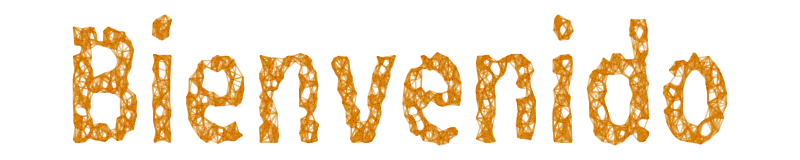

```mathematica
GrafoString["Bienvenido"]
```

```mathematica
A = {{1,2},{3,2},{2,5}};
(*Este comando le da vuelta a la lista, no a los elementos*)

Reverse[A]
```

{{2,5},{3,2},{1,2}}

Con este comando el eje X pasa a ser el eje Y, el eje Y pasa a ser el X

```mathematica
Reverse /@ A
```

{{2,1},{2,3},{5,2}}

## Comandos de operaciones con matrices

```mathematica
InterseccionBooleana
```

```mathematica
UnionBooleana
```

```mathematica
ComplementoBooleano
```

```mathematica
ProductoBooleano
```

```mathematica
Transpose
```

## Comandos de operaciones con relaciones

```mathematica
Intersection
```

```mathematica
Union
```

```mathematica
Complement
```

```mathematica
RelacionComposicion
```

```mathematica
Reverse /@
```

```mathematica
A={9,106,132,18,28,44,72,61,94,2};

R={{2,2},{2,18},{2,94},{9,9},{9,106},{18,2},{18,18},{18,94},{28,28},{44,44},{44,61},{61,44},{61,61},{72,72},{94,2},{94,18},{94,94},{106,9},{106,106},{132,132}};

ClasesEquivalencia[R,A]
```

[9]={9,106}

[106]={9,106}

[132]={132}

[18]={18,94,2}

[28]={28}

[44]={44,61}

[72]={72}

[61]={44,61}

[94]={18,94,2}

[2]={18,94,2}

El conjunto de clases de equivalencia distintas es:

{{9,106},{132},{18,94,2},{28},{44,61},{72}}

```mathematica
-Graphics--Graphics-
```

```mathematica
A={46,31,40,66,30,37};

R={{40,40},{66,40},{30,46},{66,46},{40,30},{31,30},{31,46},{37,37},{46,40},{37,31},{46,46},{30,37},{31,37},{66,30},{30,66}};

MR=MatrizRelBin[R,A,A]
```

(1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1)

```mathematica
A= Range[-30, 996,18];
B= Range[-30,998, 4];
Length[PC[A,B]]
PC[A,B]//Length
```

14964

14964

```mathematica
A={100,8,55,34,81,1,39,87,53,16};

B={13,62,21,66,44,88,93,95,80,16};

H={22,64,5,18,95,72,52,44,98,10};

R1={{8,88},{100,80},{53,80},{100,44},{87,93},{53,16},{8,93},{87,13},{1,62},{100,93}};

R2={{16,22},{95,98},{88,10},{66,5},{80,72},{21,22},{88,44},{62,72},{80,22},{66,72}};
```

```mathematica
MR1=MatrizRelBin[R1,A,B][[1]];

MR2=MatrizRelBin[R2,B,H][[1]];

R=RelBinMatriz[ProductoBooleano[MR1,MR2][[1]],A,H]
```

{{1,72},{8,10},{8,44},{53,22},{53,72},{100,22},{100,72}}

```mathematica
R=RelacionComposicion[R2,R1];
```

```mathematica
opciones = {{100,72},{34,10},{53,22},{39,64},{87,95},{1,72}};
Table[i->ElementRelBinQ[R,i],{i,opciones}]
```

{{100,72}→True,{34,10}→False,{53,22}→True,{39,64}→False,{87,95}→False,{1,72}→True}